## functions

```mathematica
DateDifferenceInUnits[date1_DateObject,date2_DateObject,unit_]:=QuantityMagnitude[DateDifference[date1,date2,unit]]
```

```mathematica
PrecedingVal[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestVal,
list[[nearestPos-1]]
]
]
```

```mathematica
PrecedingPos[list_,val_]:=Module[
{nearestVal,nearestPos},
nearestVal=Nearest[list,val][[1]];
nearestPos=Position[list,nearestVal][[1]][[1]];
If[
nearestVal<val,
nearestPos,
nearestPos-1
]
]
```

```mathematica
SparseTimeMovingAverage[data_List,windowSize_?NumericQ]:=Module[{times,values,averageValues,result,halfWindow,timeWindowIndices},(*Extract times and values*){times,values}=Transpose[data];
(*Half of the window size*)halfWindow=windowSize/2;
(*Moving average calculation*)averageValues=Table[(*Find indices of times within the window around the current time point*)timeWindowIndices=Flatten[Position[times,_?(Abs[#-times[[i]]]<=halfWindow&)]];
If[Length[timeWindowIndices]>0,Mean[values[[timeWindowIndices]]],(*Calculate mean if indices are found*)values[[i]] (*Use current value if no other values are in the window*)],{i,Length[times]}];
(*Combine times with calculated averages*)result=Transpose[{times,averageValues}]]
```

## gas

```mathematica
pulseFactor=0.1;(*one pulse equals this many m3*)
```

```mathematica
energyContentInGasPerCubicMeter=1000 34/3600;(*kWh*)
```

```mathematica
voltageTimestamps=StringSplit[Import[NotebookDirectory[]<>"gas_pulse_times.txt"],"\n"];
```

```mathematica
startDate=DateObject[voltageTimestamps[[1]]]
```

Wed 22 Nov 2023 17:11:33GMT+1

```mathematica
startDate=DateObject["2023.11.24. 00:00"]
```

Minute: Fri 24 Nov 2023 00:00GMT+1

```mathematica
timeGranularity="Minute";
```

```mathematica
voltageTimes=Map[
Round[DateDifferenceInUnits[startDate,DateObject[#],timeGranularity]]
&,voltageTimestamps];
```

```mathematica
gasTimes=Map[Round[DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity]]&,Select[Transpose[{Drop[voltageTimestamps,1],Differences[voltageTimes]}],1<#[[2]]&]];
```

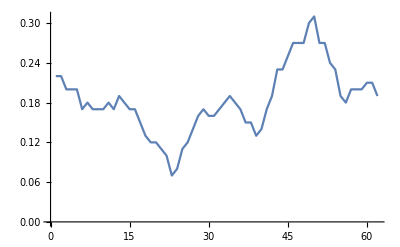

```mathematica
ListPlot[MovingAverage[BinCounts[gasTimes,{0,Max[gasTimes],10}]pulseFactor,10],Joined->True]
```

```mathematica
burntVolume=Total[BinCounts[gasTimes,{0,Max[gasTimes],10}]pulseFactor]
energyContentInBurntGas=burntVolume energyContentInGasPerCubicMeter
price=burntVolume 11 35+burntVolume 30
```

13.3

125.611

5519.5

## heat

```mathematica
groundTruth={
{3786,5334},
{1585,8044},
{222,6678},
{44,1044}
};(*fűtési, hűtési*)
```

```mathematica
FormatHeatmeterEntry[entry_]:=Module[
{list},
list=StringSplit[entry,""]/.{"-"->-1};
Table[
If[list[[pos]]==-1,
Nothing,
If[
1<pos&&list[[pos-1]]==-1,
-ToExpression[list[[pos]]],
ToExpression[list[[pos]]]
]]
,{pos,1,Length[list]}]
]
```

```mathematica
startDate=DateObject["2023.11.24. 00:00"];
```

```mathematica
timeGranularity="Minute";
```

```mathematica
readout=Map[
Join[
{Round[DateDifferenceInUnits[startDate,DateObject[#[[1]]],timeGranularity],0.25]},
Map[
FormatHeatmeterEntry[#]
&,#[[2;;5]]]
]
&,Map[
StringSplit[#,","]
&,StringSplit[Import[NotebookDirectory[]<>"heatmeter_readouts.csv","Text"],"\n"]]];
```

```mathematica
heatingCumulativeUnclean=Table[DeleteDuplicates[Select[Map[
{#[[1]],ToExpression[StringRiffle[#[[2]],""]]}&,
Select[
Transpose[Transpose[readout][[{1,cycle+1}]]],
MemberQ[#[[2]],-1]==False&
]],#[[2]]-groundTruth[[cycle]][[1]]<1500&]],{cycle,1,4}];
```

```mathematica
heatingCumulativeClean=Table[Table[
If[
10<Abs[heatingCumulativeUnclean[[cycle]][[n]][[2]]-heatingCumulativeUnclean[[cycle]][[n-1]][[2]]],
Nothing,
heatingCumulativeUnclean[[cycle]][[n]]
]
,{n,2,Length[heatingCumulativeUnclean[[cycle]]]}],{cycle,1,4}];
```

```mathematica
energyContentDeliveredOnCycles=Total[Quiet[Select[Table[
Select[heatingCumulativeClean[[cycle]],0<#[[1]]&]//#[[-1]][[2]]-#[[1]][[2]]&
,{cycle,1,4}],Positive]]]
```

93

```mathematica
efficiency=100 energyContentDeliveredOnCycles/energyContentInBurntGas
```

74.038

```mathematica
heatingDiff=Table[Table[
{Mean[{heatingCumulativeClean[[cycle]][[n]][[1]],heatingCumulativeClean[[cycle]][[n-1]][[1]]}],(heatingCumulativeClean[[cycle]][[n]][[2]]-heatingCumulativeClean[[cycle]][[n-1]][[2]])/(heatingCumulativeClean[[cycle]][[n]][[1]]-heatingCumulativeClean[[cycle]][[n-1]][[1]])}
,{n,2,Length[heatingCumulativeClean[[cycle]]]}],{cycle,1,4}];
```

Power::infy: Infinite expression 1/0. encountered.

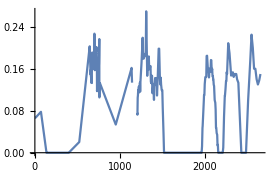
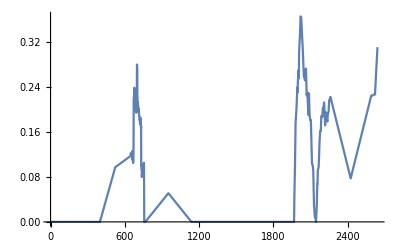
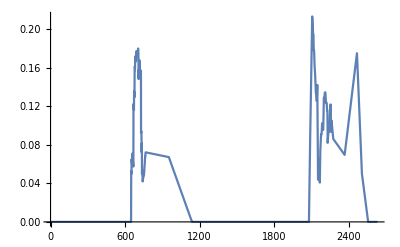
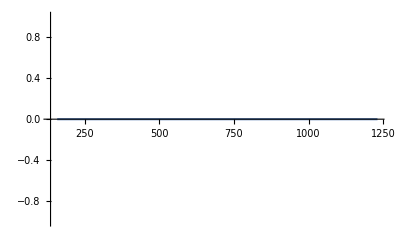

```mathematica
Table[
ListPlot[SparseTimeMovingAverage[heatingDiff[[cycle]],60 1],Joined->True,PlotRange->All]
,{cycle,1,4}]
```

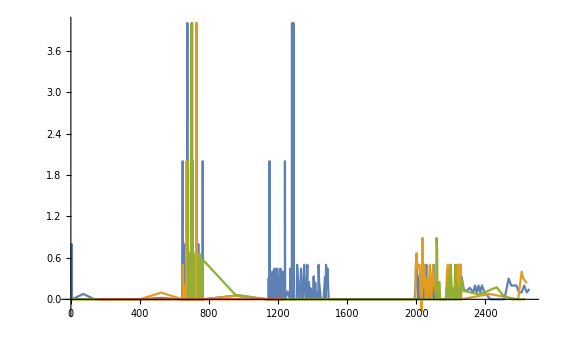

```mathematica
ListPlot[heatingDiff,Joined->True,PlotRange->All]
```